```mathematica
sigma0=10^6
gamma0=100
```

```mathematica
sigma0=10^4
gamma0=100
```

10000

100

```mathematica
sigmainf=(sigma0*gamma0)^(2/3.)
sigmainf/10^5
gammainf=(sigma0*gamma0)^(1/3.)
```

10000.

0.1

100.

```mathematica
rho=0.001914
1/rho
```

0.001914

522.466

```mathematica
sigma0=4*10^4
gamma0=(sigma0)^(1.0/2.0)
```

40000

200.

```mathematica
VR=2000*km
VR/c
```

200000000

0.00667128

```mathematica
T=(2009-1054)*365.25*24*60*60
```

3.01375×10^10

```mathematica
VR*T
```

6.0275×10^18

```mathematica
VS=3*10^(17)/T
VS/c
```

9.95437×10^6

0.000332042

```mathematica
Lnow=5*10^(38)
rn=2*pc
```

500000000000000000000000000000000000000

6.172×10^18

```mathematica
Lnow*T
```

1.50688×10^49

```mathematica
Solve[Lnow/(c*4*Pi*rs^2)==Lnow*T/(4/3*Pi*rn^3),rs]
```

{{rs→-2.9452×10^17},{rs→2.9452×10^17}}

```mathematica
3*10^17/T/c
```

0.000332042

```mathematica
myrs=2.945196176033979*^17
myrs/rn
```

2.9452×10^17

0.0477187

```mathematica
pinner=Lnow/(c*4*Pi*myrs^2)
pouter=Lnow*T/(4/3*Pi*rn^3)
```

1.53007×10^-8

1.53007×10^-8

```mathematica
Solve[pouter==rhos*VS^2,rhos]
```

{{rhos→1.54413×10^-22}}

```mathematica
myrhos=1.5441274710604203*^-22
myns=myrhos/mb
myrhos*c^2
```

1.54413×10^-22

92.2542

0.138779

```mathematica
Bs=4*10^(12)/r
Eb=Bs^2/(8*Pi)
sigma=Eb/(myrhos*c^2)//.{r->myrs}
```

4000000000000/r

2000000000000000000000000/(π r^2)

5.28843×10^-11

```mathematica
rhotest=1*mb
sigmatest=Eb/(rhotest*c^2)
```

1.67377×10^-24

4.23196×10^26

```mathematica
rho
```

0.001914

```mathematica
Clear[rho]
```

```mathematica
(* Computation of sigma *)
(* McKinney 2006 used for A_\phi and A_\phi for last polar cap A_\phi *)
(* Daugherty & Harding 1982 is used for Crab particle flux Ndot=3E37/s from secondary particle flux *)
```

```mathematica
Bgauss=3.8*10^(12)
Bhl=Bgauss/Sqrt[4*Pi]
Bs=Bhl
tau=33/1000
omega=2*Pi/tau
rstar=10*km
(*Ndot=3*10^(37)*) (* DH82 *)
Ndot=1.8*10^(39) (* HA01 *)
(*Ndot=10^(41)*) (* Sturrock *)
(* lab-frame grams/second *)
Mdot=Ndot*me
vp=c
SA=Integrate[2*Pi*r^2*Sin[th2],{th2,0,th}]
Efluxsurf=gamma^2*(rho*c^2*vp*SA)
(* total particle flux only from polar cap at fixed rate*)
(* Note that particle flux is \rho u^r = \rho \gamma v^r *)
(* The particle mass rate is Mdot=4\pi r^2 \rho \gamma v^r *)
Edot=Mdot*gamma*c^2
(*Sdot=(r*omega/c*Sin[th]*Bs)^2*c*SA*)
Sdot=Integrate[2*Pi*r^2*Sin[th2]*(r*omega/c*Sin[th2]*Bs)^2*c,{th2,0,th}]
sigma=Sdot/Edot
(* Get angle of polar cap *)
(* Arons defines mu=Bs*rstar^3 *)
mu=Bs*rstar^3/2
Print["Aphi0"];
(* Aphi for last open field line *)
Aphi0=1.226*mu*omega/c
Rlc=c/omega
Aphi=Bs/(2*r)*rstar^3*Sin[th]^2
Print["Aphilc"];
Aphilc=Aphi//.{r->Rlc}
Print["Aphistar"];
Aphistar=Aphi//.{r->rstar}
eq1=Aphi0==Aphistar
sol=FindRoot[eq1,{th,0.1}]
myth=sol[[1,2]]
Print["th degrees"];
thetadeg=myth*180/Pi
Print["Rcl/rstar"];
Rlc/rstar
myrs/Rlc
Print["NdotGJ1"];
NdotGJ1=2*c/q*(omega^2*mu/c^2)
Print["ndengj"];
ndengj=omega*Bs/(2*Pi*c*q)
rhogj=ndengj*me
```

3.8×10^12

1.07196×10^12

1.07196×10^12

33/1000

(2000 π)/33

1000000

1.8×10^39

1.63969×10^12

2.99792×10^10

-2 π r^2 (-1+Cos[th])

-1.69294×10^32 gamma^2 r^2 rho (-1+Cos[th])

1.47368×10^33 gamma

-8.73069×10^18 r^4 (-1.+Cos[th]) Sin[2 th]^2

-(5.92442×10^-15 r^4 (-1.+Cos[th]) Sin[2 th]^2)/gamma

5.3598×10^29

Aphi0

4.17335×10^21

1.57454×10^8

(5.3598×10^29 Sin[th]^2)/r

Aphilc

3.40403×10^21 Sin[th]^2

Aphistar

5.3598×10^23 Sin[th]^2

4.17335×10^21==5.3598×10^23 Sin[th]^2

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{th→0.0883554}

0.0883554

th degrees

5.06239

Rcl/rstar

157.454

6.35105×10^-9 myrs

NdotGJ1

2.6989×10^33

ndengj

2.25601×10^12

2.05508×10^-15

```mathematica
q
```

4.8029×10^-10

```mathematica
1/c
```

3.33564×10^-11

```mathematica
0.1*pc/rstar
```

3.086×10^11

```mathematica
(* Effective equatorial sigma for monopole model of pulsar *)
sigmaconsts={r->rstar,th->myth,gamma->1000.0}
mysigma0=sigma//.sigmaconsts
Edot//.sigmaconsts
Sdot//.sigmaconsts
mysigma0/10^2
```

{r→1000000,th→0.0883554,gamma→1000.}

714.167

1.47368×10^36

1.05245×10^39

7.14167

```mathematica
1/0.001914
```

522.466

```mathematica
(* my Gaussian magnetic moment in cgs *)
mu*Sqrt[4*Pi]*1.0
(* off compared to Arons paper giving 3.6E30 *)
```

2.×10^30

```mathematica
(* Gaussian and HL units conversion *)
Clear[Bhl]
Solve[Bg^2/(8*Pi)==Bhl^2/(2),Bhl]
```

{{Bhl→-Bg/(2 √π)},{Bhl→Bg/(2 √π)}}

```mathematica
it={{10,0.5},{100,10},{1000,10^(-1)},{10^4,10^(-4)}}
```

{{10,0.5},{100,10},{1000,1/10},{10000,1/10000}}

```mathematica
it={{10,0.5*10},{40,70*40},{100,10*100},{1000,10^(-1)*1000},{10^4,10^(-4)*10^4}}
```

{{10,5.},{40,2800},{100,1000},{1000,100},{10000,1}}

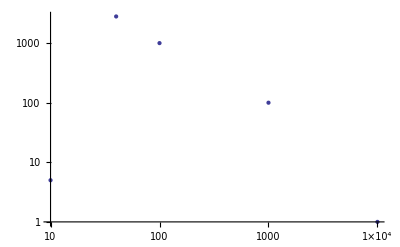

```mathematica
ListLogLogPlot[it]
```

```mathematica
5*Pi/180.
```

0.0872665

```mathematica
gamma1=5.05*10^6*(Bs/10^(12))^(1/6)*(tau)^(-5/12)
```

2.13462×10^7

```mathematica
(10.0)^(1/3)
```

2.15443

```mathematica
.03*180/Pi
```

1.71887

```mathematica
pow=1.5
n=(e/e0)^(-pow)
crap=(n/e)//.{e->40}
mye0=Solve[crap==100,e0][[1,1,2]]
nnew=n//.{e0->mye0}
D[nnew,e]
```

1.5

1/(e/e0)^1.5

0.0000988212/(1/e0)^1.5

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

10079.4

(1.01193×10^6)/e^1.5

-(1.51789×10^6)/e^2.5

```mathematica
nnew/e
```

(1.01193×10^6)/e^2.5

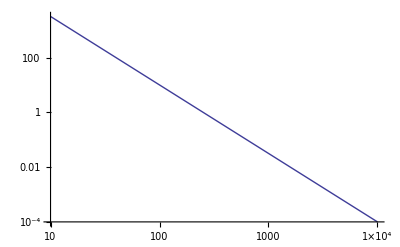

```mathematica
LogLogPlot[{nnew/e},{e,10,10^4}]
```

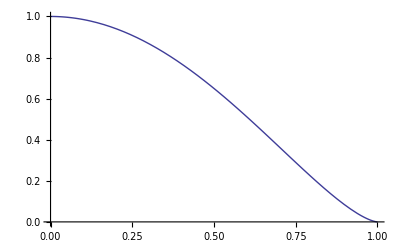

```mathematica
Plot[(1-x^2)^(3/2),{x,0,1}]
```

```mathematica
(* Get \gamma_{\infty} *)
```

```mathematica
Clear[r,thetaj,gammainf,mu,sigma]
Clear[mu,omegastar,thetaj]
factor1=2^(3/2)*Log[omegastar*r*Sin[thetaj]/mu^(1/3)]^(1/2)
(*factor2=2*Log[omegastar*r*Sin[thetaj]/mu^(1/3)]^(1/3)*)
ONE=1
gammainfeq=gammainf==sigma^(1/2)*factor1/(Sin[thetaj])^(1)//.{sigma->mu/gammainf-ONE}
sol=Solve[{gammainfeq},gammainf]
mygammainf=sol[[1,1,2]]
```

2 √2 √Log[(omegastar r Sin[thetaj])/mu^(1/3)]

1

gammainf==2 √2 √(-1+mu/gammainf) Csc[thetaj] √Log[(omegastar r Sin[thetaj])/mu^(1/3)]

{{gammainf→-(4 (2/3)^(1/3) Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)])/(9 mu Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)]+√3 √(27 mu^2 Csc[thetaj]^4 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^2+32 Csc[thetaj]^6 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^3))^(1/3)+(2/3)^(2/3) (9 mu Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)]+√3 √(27 mu^2 Csc[thetaj]^4 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^2+32 Csc[thetaj]^6 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^3))^(1/3)},{gammainf→(2 (2/3)^(1/3) (1+ⅈ √3) Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)])/(9 mu Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)]+√3 √(27 mu^2 Csc[thetaj]^4 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^2+32 Csc[thetaj]^6 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^3))^(1/3)-1/(2^(1/3) 3^(2/3))(1-ⅈ √3) (9 mu Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)]+√3 √(27 mu^2 Csc[thetaj]^4 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^2+32 Csc[thetaj]^6 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^3))^(1/3)},{gammainf→(2 (2/3)^(1/3) (1-ⅈ √3) Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)])/(9 mu Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)]+√3 √(27 mu^2 Csc[thetaj]^4 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^2+32 Csc[thetaj]^6 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^3))^(1/3)-1/(2^(1/3) 3^(2/3))(1+ⅈ √3) (9 mu Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)]+√3 √(27 mu^2 Csc[thetaj]^4 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^2+32 Csc[thetaj]^6 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^3))^(1/3)}}

-(4 (2/3)^(1/3) Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)])/(9 mu Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)]+√3 √(27 mu^2 Csc[thetaj]^4 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^2+32 Csc[thetaj]^6 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^3))^(1/3)+(2/3)^(2/3) (9 mu Csc[thetaj]^2 Log[(omegastar r Sin[thetaj])/mu^(1/3)]+√3 √(27 mu^2 Csc[thetaj]^4 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^2+32 Csc[thetaj]^6 Log[(omegastar r Sin[thetaj])/mu^(1/3)]^3))^(1/3)

```mathematica
consts={mu->mu1000*1000,omegastar->omegapt25*0.25,
thetaj->thetaj5deg*5*Pi/180.,r->r10*10^(10),mu1000->.3,omegapt25->1,thetaj5deg->4/5,r10->1/100}
result=mygammainf//.consts
eff=(mygammainf/mu)//.consts
result*thetaj//.consts
```

{mu→1000 mu1000,omegastar→0.25 omegapt25,thetaj→0.0872665 thetaj5deg,r→10000000000 r10,mu1000→0.3,omegapt25→1,thetaj5deg→4/5,r10→1/100}

146.534

0.488446

10.23

```mathematica
consts={mu->mu1000*1000,omegastar->omegapt25/4,
thetaj->thetaj5deg*5*Pi/180,r->r10*10^(10),mu1000->1,omegapt25->1,r10->1/100};
result=mygammainf//.consts;
product=result*thetaj//.consts;
```

0.01

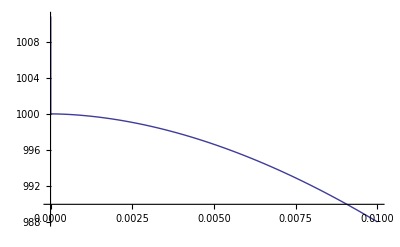

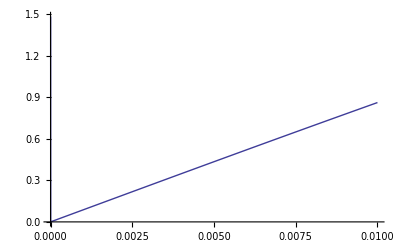

```mathematica
thetaj5degout=0.01
Plot[result,{thetaj5deg,0,thetaj5degout}]
Plot[product,{thetaj5deg,0,thetaj5degout}]
```

```mathematica
Limit[result,thetaj5deg->0]
```

$Aborted

```mathematica
FindRoot[0==D[result,thetaj5deg],{thetaj5deg,0.1}]
```

{thetaj5deg→18.}

```mathematica
M=1*msun
rl=G*M/c^2
```

1.989×10^33

147655.

```mathematica
10^(16)/rl
```

6.77252×10^10

```mathematica
sigma0=10^6
gamma0=10^3.
rf=Sqrt[sigma0/gamma0]
```

1000000

1000.

31.6228